```mathematica
ClearAll["Global`*"]
```

```mathematica
Layers=3;
```

```mathematica
hbar=1.0545717 10^-27;
clight=29979245800.;
e=4.80320425 10^-10;
eV=e 1./300.;
nm=10^-7;
```

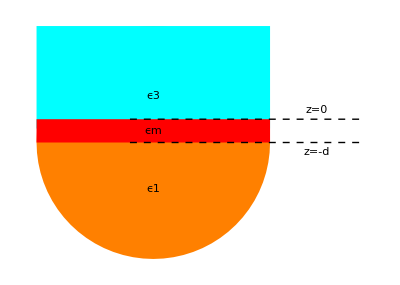

```mathematica
Graphics[{Orange,Disk[{-.5,0},2.5,{-Pi,Pi}],(*Thick,Green,Rectangle[{-3,-1},{2,.3}],*)Thick,Cyan,Rectangle[{-3,2.5},{2,.3}],Thick,Red,Rectangle[{-3,0},{2,.5}],Orange,Black,Dashed,Line[{{-1,0},{4,0}}],Line[{{-1,.5},{4,.5}}]},Epilog->{Text[Style["ϵm"],{-0.5,.25}],Text[Style["ϵ1"],{-.5,-1}],Text[Style["ϵ3"],{-.5,1}],Text[Style["z=-d"],{3,-.2}],Text[Style["z=0"],{3,.7}]},BaseStyle->{FontFamily->"Helvetica",FontSize->16,Black}]
```

```mathematica
(*Defining the variables*)
μ[i_]:=1;
params={ϵ[1]->3.2(*glass*),ϵ[3]->2(*heavy glass*),ϵ[2]->(-10.91+0.83ⅈ)(*(*-15*)(1-(ωp/ω)^2)*)(*metal*)};
vars1=Flatten[Table[{ϵ[i](*,κ[i]*),u[i],A[i],B[i]},{i,Layers+3}]];
vars2=ToExpression[Flatten[Table[{StringJoin[ToString[ϵ],ToString[i]](*,StringJoin[ToString[κ],ToString[i]]*),StringJoin[ToString[u],ToString[i]],StringJoin[ToString[A],ToString[i]],StringJoin[ToString[B],ToString[i]]},{i,Layers+3}]]];
vars11=Flatten[Append[{E0[y,0],E0[0,z]},vars1]];
vars12=Flatten[Append[{E0y,E0z},vars2]];
Evaluate[vars11]=vars12
```

{E0y,E0z,ϵ1,u1,A1,B1,ϵ2,u2,A2,B2,ϵ3,u3,A3,B3,ϵ4,u4,A4,B4,ϵ5,u5,A5,B5,ϵ6,u6,A6,B6}

```mathematica
params1={A1->1,B1->r,A3->t,A4->0,B4->r,A6->t};
```

```mathematica
(*Field Equations*)
```

```mathematica
(*Helmholtz1[index_]:=k0^2 ϵ[index]μ[index]-k^2+κ[index]^2 (*helmholtz equation*)*)

Hfieldin[z_,index_]:={Piecewise[{{A[index] ⅇ^(ⅈ κ[index](z(*-d*)))ⅇ^(ⅈ k y (*-ⅈ ω t*))(*E0[z]*),index==3}},(A[index] ⅇ^(ⅈ κ[index]z)+B[index] ⅇ^(- ⅈ κ[index]z))ⅇ^(ⅈ k y (*-ⅈ ω t*))],0,0}  (*Transverse field along x*)
(*Hfieldsc[z_,index_]:={Piecewise[{{A[index+Layers] ⅇ^(ⅈ κ[index+Layers](z-d)) ⅇ^(ⅈ k y (*-ⅈ ω t*))(*E0[z]*),index==3}},(A[index+Layers] ⅇ^(ⅈ κ[index+Layers]z)+B[index+Layers] ⅇ^(- ⅈ κ[index+Layers]z))ⅇ^(ⅈ k y (*-ⅈ ω t*))],0,0}  (*Transverse field along x*)*)

(*Efields corresponding to it in different directions*)
Efieldin[z_,index_]=ⅈ/(k0  ϵ[index])Curl[Hfieldin[z,index],{x,y,z}]/.{D[E0[z],z]:>0};
(*Efield2[z_,index_]=ⅈ/(k0  ϵ[index])Curl[Hfieldsc[z,index],{x,y,z}]/.{D[E0[z],z]:>0};*)
```

```mathematica
Table[Hfieldin[z,i]/.params1,{i,1,3}](*Magnetic Field *)
```

{{ⅇ^(ⅈ k y) (ⅇ^(ⅈ z κ[1])+ⅇ^(-ⅈ z κ[1]) r),0,0},{ⅇ^(ⅈ k y) (B2 ⅇ^(-ⅈ z κ[2])+A2 ⅇ^(ⅈ z κ[2])),0,0},{ⅇ^(ⅈ k y+ⅈ z κ[3]) t,0,0}}

```mathematica
Table[Efieldin[z,i]/.params1,{i,1,3}](*Electric Field*)//Simplify
```

{{0,-(ⅇ^(ⅈ (k y-z κ[1])) (ⅇ^(2 ⅈ z κ[1])-r) κ[1])/(k0 ϵ1),(ⅇ^(ⅈ (k y-z κ[1])) k (ⅇ^(2 ⅈ z κ[1])+r))/(k0 ϵ1)},{0,-(ⅇ^(ⅈ (k y-z κ[2])) (-B2+A2 ⅇ^(2 ⅈ z κ[2])) κ[2])/(k0 ϵ2),(ⅇ^(ⅈ (k y-z κ[2])) (B2+A2 ⅇ^(2 ⅈ z κ[2])) k)/(k0 ϵ2)},{0,-(ⅇ^(ⅈ (k y+z κ[3])) t κ[3])/(k0 ϵ3),(ⅇ^(ⅈ (k y+z κ[3])) k t)/(k0 ϵ3)}}

```mathematica
(*Boundary Conditions*)
```

```mathematica
(*<<EqualThread.m*)
```

```mathematica
d1={-d,0};
(*Maxwell Boundary condition at two interfaces d=0 and d=d*)
eqns=Flatten[{(*eqnhelm*){},Flatten[Table[{Hfieldin[d1[[k1]],k1][[1]]==Hfieldin[d1[[k1]],k1+1][[1]],Efieldin[d1[[k1]],k1][[2]]==Efieldin[d1[[k1]],k1+1][[2]]},{k1,Layers-1}]]}]/.params1/.y->0
```

{ⅇ^(-ⅈ d κ[1])+ⅇ^(ⅈ d κ[1]) r==A2 ⅇ^(-ⅈ d κ[2])+B2 ⅇ^(ⅈ d κ[2]),(ⅈ (ⅈ ⅇ^(-ⅈ d κ[1]) κ[1]-ⅈ ⅇ^(ⅈ d κ[1]) r κ[1]))/(k0 ϵ1)==(ⅈ (ⅈ A2 ⅇ^(-ⅈ d κ[2]) κ[2]-ⅈ B2 ⅇ^(ⅈ d κ[2]) κ[2]))/(k0 ϵ2),A2+B2==t,(ⅈ (ⅈ A2 κ[2]-ⅈ B2 κ[2]))/(k0 ϵ2)==-(t κ[3])/(k0 ϵ3)}

```mathematica
complexInner[a_]:={Conjugate[a]}.{a};
```

```mathematica
(*variables*)
Var={A2,t,r,B2};
(*solutions*)
s=Solve[eqns, Var]//FullSimplify;
(*κ[i_]:=ξ[i]ϵ[i]*)
s
```

{{A2→(ⅈ ⅇ^(-ⅈ d κ[1]) ϵ2 κ[1] (ϵ3 κ[2]+ϵ2 κ[3]))/(ⅈ ϵ2 Cos[d κ[2]] κ[2] (ϵ3 κ[1]+ϵ1 κ[3])+Sin[d κ[2]] (ϵ1 ϵ3 κ[2]^2+ϵ2^2 κ[1] κ[3])),t→(4 ⅇ^(-ⅈ d (κ[1]-κ[2])) ϵ2 ϵ3 κ[1] κ[2])/(ⅇ^(2 ⅈ d κ[2]) (ϵ2 κ[1]-ϵ1 κ[2]) (ϵ3 κ[2]-ϵ2 κ[3])+(ϵ2 κ[1]+ϵ1 κ[2]) (ϵ3 κ[2]+ϵ2 κ[3])),r→(ⅇ^(-2 ⅈ d κ[1]) (ⅇ^(2 ⅈ d κ[2]) (ϵ2 κ[1]+ϵ1 κ[2]) (ϵ3 κ[2]-ϵ2 κ[3])+(ϵ2 κ[1]-ϵ1 κ[2]) (ϵ3 κ[2]+ϵ2 κ[3])))/(-ⅇ^(2 ⅈ d κ[2]) (ϵ2 κ[1]-ϵ1 κ[2]) (-ϵ3 κ[2]+ϵ2 κ[3])+(ϵ2 κ[1]+ϵ1 κ[2]) (ϵ3 κ[2]+ϵ2 κ[3])),B2→(2 ⅇ^(-ⅈ d (κ[1]-κ[2])) ϵ2 κ[1] (-ϵ3 κ[2]+ϵ2 κ[3]))/(ⅇ^(2 ⅈ d κ[2]) (ϵ2 κ[1]-ϵ1 κ[2]) (-ϵ3 κ[2]+ϵ2 κ[3])-(ϵ2 κ[1]+ϵ1 κ[2]) (ϵ3 κ[2]+ϵ2 κ[3]))}}

```mathematica
(*solution from solving Maxwell BCs*)
Rcoeffr=r/.s//FullSimplify(* reflectioncoefficient*)
Reflectancesq=complexInner[Rcoeffr[[1]]]/.s(*r^2*);
```

{(ⅇ^(-2 ⅈ d κ[1]) (ⅇ^(2 ⅈ d κ[2]) (ϵ2 κ[1]+ϵ1 κ[2]) (ϵ3 κ[2]-ϵ2 κ[3])+(ϵ2 κ[1]-ϵ1 κ[2]) (ϵ3 κ[2]+ϵ2 κ[3])))/(-ⅇ^(2 ⅈ d κ[2]) (ϵ2 κ[1]-ϵ1 κ[2]) (-ϵ3 κ[2]+ϵ2 κ[3])+(ϵ2 κ[1]+ϵ1 κ[2]) (ϵ3 κ[2]+ϵ2 κ[3]))}

```mathematica
(*noginov Solution*)
Rcoeffrnoi=(r[1,2]+r[2,3] ⅇ^(2 ⅈ κ[2]d))/(1+r[1,2] r[2,3] ⅇ^(2 ⅈ κ[2]d));
r[i_,j_]:=(κ[i]ϵ[j]-κ[j]ϵ[i])/(κ[i]ϵ[j]+κ[j]ϵ[i]) 
ReflectancesqNonigov=complexInner[Rcoeffrnoi];
```

```mathematica
(*(Rcoeffr-Rcoeffrnoi)//FullSimplify(*comparision of our solution to nonigov's*)*)
```

```mathematica
κ[index_]:= Sqrt[k0^2 ϵ[index]μ[index]-k^2 ](*helmholtz equation*)
```

```mathematica
Refc[d_]=Reflectancesq[[1]]
Refc1[d_]=ReflectancesqNonigov/.params;
```

(ⅇ^(-2 ⅈ d √(-k^2+k0^2 ϵ1)+2 ⅈ Conjugate[d √(-k^2+k0^2 ϵ1)]) (ⅇ^(2 ⅈ d √(-k^2+k0^2 ϵ2)) (√(-k^2+k0^2 ϵ1) ϵ2+ϵ1 √(-k^2+k0^2 ϵ2)) (√(-k^2+k0^2 ϵ2) ϵ3-ϵ2 √(-k^2+k0^2 ϵ3))+(√(-k^2+k0^2 ϵ1) ϵ2-ϵ1 √(-k^2+k0^2 ϵ2)) (√(-k^2+k0^2 ϵ2) ϵ3+ϵ2 √(-k^2+k0^2 ϵ3))) Conjugate[ⅇ^(2 ⅈ d √(-k^2+k0^2 ϵ2)) (√(-k^2+k0^2 ϵ1) ϵ2+ϵ1 √(-k^2+k0^2 ϵ2)) (√(-k^2+k0^2 ϵ2) ϵ3-ϵ2 √(-k^2+k0^2 ϵ3))+(√(-k^2+k0^2 ϵ1) ϵ2-ϵ1 √(-k^2+k0^2 ϵ2)) (√(-k^2+k0^2 ϵ2) ϵ3+ϵ2 √(-k^2+k0^2 ϵ3))])/((-ⅇ^(2 ⅈ d √(-k^2+k0^2 ϵ2)) (√(-k^2+k0^2 ϵ1) ϵ2-ϵ1 √(-k^2+k0^2 ϵ2)) (-√(-k^2+k0^2 ϵ2) ϵ3+ϵ2 √(-k^2+k0^2 ϵ3))+(√(-k^2+k0^2 ϵ1) ϵ2+ϵ1 √(-k^2+k0^2 ϵ2)) (√(-k^2+k0^2 ϵ2) ϵ3+ϵ2 √(-k^2+k0^2 ϵ3))) Conjugate[-ⅇ^(2 ⅈ d √(-k^2+k0^2 ϵ2)) (√(-k^2+k0^2 ϵ1) ϵ2-ϵ1 √(-k^2+k0^2 ϵ2)) (-√(-k^2+k0^2 ϵ2) ϵ3+ϵ2 √(-k^2+k0^2 ϵ3))+(√(-k^2+k0^2 ϵ1) ϵ2+ϵ1 √(-k^2+k0^2 ϵ2)) (√(-k^2+k0^2 ϵ2) ϵ3+ϵ2 √(-k^2+k0^2 ϵ3))])

```mathematica
c=29979245800.;
ωp=(*9.6 eV/hbar*)9.6 eV/hbar;
ω=(*1.5 eV/hbar*)1.5 eV/hbar;
k0= (ω/c);
ls=25 nm;
k=(√ϵ[1]) k0  Sin[θ]/.params;
```

```mathematica
(*Plotting*)
Tab1=Table[Table[{θ 180/π,Refc[d]/.params},{θ,0,π/2,1/100}],{d,50nm,70nm ,10nm}];
```

```mathematica
Tab2=Table[{θ 180/π ,Refc1[70nm]},{θ,0,π/2,1/100}];
```

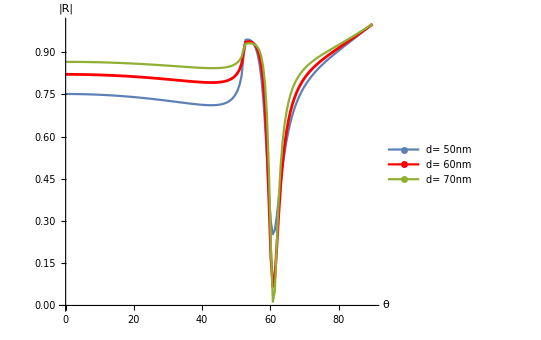

```mathematica
ListLinePlot[Flatten[Tab1,1,1],PlotRange->All,AxesLabel->{"θ","|R|"},AspectRatio->0.85,
PlotLegends->{Placed[LineLegend[{"d= 50nm","d= 60nm","d= 70nm"},LegendMarkers->Graphics[{Thickness[0.1],Line[{{1,0},{9,0}}]}]],(*{Right,Bottom}*){.33,.4}]},PlotStyle->{{Green,Thickness->0.005}{Blue,Thickness->0.005},{Red,Thickness->0.005}},AxesStyle->{{Directive[Black],Thickness->0.004},{Directive[Black],Thickness->0.004}},BaseStyle->{FontSize->18},ImageSize->400]
```

```mathematica
Tab3=Table[{θ 180/π ,Refc[70nm]},{θ,0,π/2,1/100}];
```

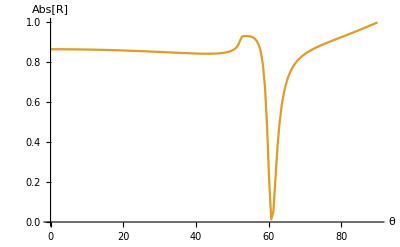

```mathematica
ListLinePlot[{Tab3,Tab2},PlotRange->All,AxesLabel->{"θ","Abs[R]"}](*Noginov's Expression vs my expression at d=70nm Exact match*)
```

```mathematica
(*re=((ξd-ξm)(ξv+ξm)ⅇ^(-ⅈ κ[2]d)-(ξd+ξm)(ξv-ξm)ⅇ^(ⅈ κ[2]d))/((ξd+ξm)(ξv+ξm)ⅇ^(-ⅈ κ[2]d)-(ξm-ξd)(ξv-ξm)ⅇ^(ⅈ κ[2]d));
ξd=κ[3]/ϵ[3];ξv=κ[1]/ϵ[1];ξm=κ[2]/ϵ[2];
a2=re;*)
```

```mathematica
(*Nr=(zs-zm)(zm+zd)+ⅇ^(2ⅈ κ[2]d)(zs+zm)(zm-zd);
D1=(zs+zm)(zm+zd)+ⅇ^(2ⅈ κ[2]d)(zs-zm)(zm-zd);
zs= κ[1]/ϵ[1];zm=κ[2]/ϵ[2];zd=κ[3]/ϵ[3];
a2=complexInner[Nr/D1];*)
```

```mathematica
(*κ[index_]:=Sqrt[k0^2 ϵ[index]μ[index]-k^2 ]*)
```

```mathematica
(*κ[index_]:=Piecewise[{{-k0 (ϵ[index]ϵ[1])/Sqrt[ϵ[2]+ϵ[3]],index==4}},Sqrt[ϵ[index] k0^2-k^2]]*)
```